```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
qpData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,qpData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
momentumAvail= Normal[DeleteDuplicates[ds[Take,"momentum"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"momentum"->momentumAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,invX_ :True]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
If[invX,x=1/Sqrt[x]];
result=Table[{x[[it]],y[[it]]},{it,Length[x]}];
Clear[x,y];
result
)
```

```mathematica
makeFits[data_,func_,arg_,points_]:=Table[Fit[d[[-Min[points,Length[d]];;-1]],func,arg],{d, data}];
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getPlot[data_,func_, arg_,points_]:=(
SetOptions[LinTicks,TickLengthScale->2.5];
SetOptions[MaTeX,Magnification->2.14];

colors={Purple,Orange};
pltStyle=Table[Directive[color,Opacity[0.7],Dashed],{color,colors}];

fs=22;
plt=ListPlot[data,
PlotRange->{{0,0.3001},{0,0.4}},ImageSize->360,
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
PlotMarkers->{"●", 14},
(*PlotLegends->Placed[
PointLegend[Table[
Style[StringJoin["λ = ",ToString[NumberForm[B,{2,1}]]],fs,FontFamily->"BookmanOldStyle"],
{B,qpAvail["interaction"]//Normal}],Spacings->0.3],
{0.75,0.80}],*)
Epilog->Inset[
MaTeX["\\text{(b) }"],
{0.035(*0.075*),0.44*4/5}],
FrameLabel->{MaTeX["L^{-1/2}"],MaTeX["z"]},
LabelStyle->Directive[Black,12],
PlotStyle->pltStyle,
AspectRatio->.75,
FrameTicks->{{LinTicks[0,0.5,0.1,5,TickLabelFunction->tlf],StripTickLabels[LinTicks[0,0.5,0.1,5]]},{LinTicks[0,0.3,0.1, 10,TickLabelFunction->tlf],StripTickLabels[LinTicks[0,0.3,0.1, 5]]}}
];

fits=makeFits[data,func,arg,points];
fplt=Plot[fits,{x,0,0.3},PlotStyle->pltStyle];

Show[plt,fplt,PlotRangeClipping->False]
)
```

```mathematica
makePlotsZ[]:=(
fitFunctions={1,x};
fitPoints=5;

directive={Select[#coupling==J&&#momentum==k&&#interaction==B&]};
keys={"size","weight"};

plots={};
Do[(
Do[(
z={};
Do[(
AppendTo[z,extractData[qpDataset,directive,keys]];
),{B,qpAvail["interaction"]//Normal}];
AppendTo[plots,{getPlot[z,fitFunctions, x,fitPoints]}];
),{k,qpAvail["momentum"]//Normal}];
),{J,qpAvail["coupling"]//Normal}];

plots
)
```

J ∈ {0.4} @ 12-2-28_0.0-1.0-1.0

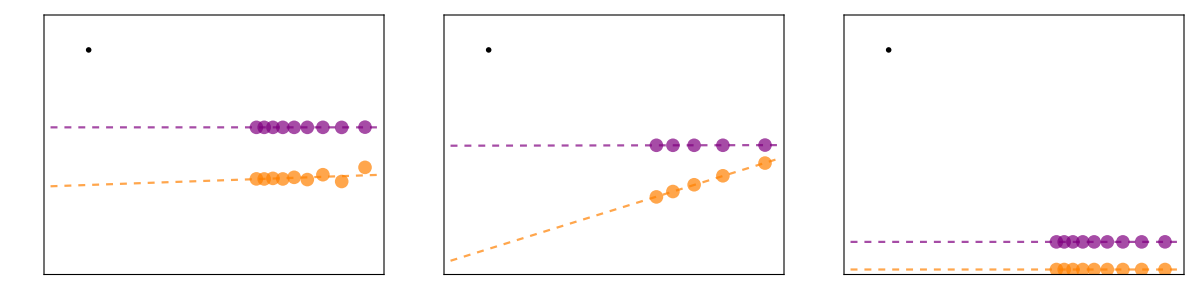

```mathematica
JRange={"0.4"};
tails={"12-2-28_0.0-1.0-1.0"};
zPlots={};
Do[(
qpDataset=Dataset[getAssoc["qp",JRange,tail]];
qpAvail=Dataset[getStruct[qpDataset]];
Print[Style[StringJoin["J ∈ ",ToString[JRange]," @ ", tail],16]];
AppendTo[zPlots,makePlotsZ[]];
kDim=Length[qpAvail["momentum"]];
plots=ArrayReshape[zPlots[[-1]],{Length[zPlots[[-1]]]/kDim,kDim}];
Print[Grid[plots]];
),{tail,tails}]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
fileName=StringJoin["plots/scaling/z/",
"z_J=",ToString[qpAvail["coupling"][[iJ]]],
"_k=",ToString[qpAvail["momentum"][[ik]]],
".jpg"];
Export[fileName,zPlots[[1,(iJ-1)*Length[qpAvail["momentum"]//Normal]+ik,1]],ImageResolution->300];
),{ik,Length[qpAvail["momentum"]//Normal]}]
),{iJ,Length[qpAvail["coupling"]//Normal]}]
)
```

```mathematica
SavePlots[]
```